```mathematica
T1[e13_,e23_,e34_,e45_]:=Catch[Module[{colc={e13,e34,e45,e23},mem={0}},
mem[[1]]=1/Mod[1/colc[[2]],1/colc[[1]]];
mem[[1]]=Floor[Mod[mem[[1]],colc[[3]]-colc[[4]]]];
Throw[mem[[1]]];
]]
```

```mathematica
ccMod=Compile[{{x,_Integer},{y,_Integer}},Mod[x,y],RuntimeOptions->"Speed"];
```

```mathematica
ccMod[11,5]
```

1

```mathematica
FactInt[zzr_,zzr2_]:=Catch[Module[{colc=zzr,colc2=zzr2,mem={0,2,0,0,0,0,0,0},mem2,mem3={0,0,0,0},dat={},dat1b={},dat2={},dat3={},cnt={0,0,1},swt={0,0}},
If[colc<5000,Throw[FactorInteger[colc]];];
mem2=Log[colc]^2;
mem[[3]]=(mem2 mem2/Log[mem2]^2);
mem[[8]]=2mem[[3]];
mem[[5]]=0;
mem3[[2]]=√colc;
mem3[[1]]=√mem3[[2]];
dat=Table[Prime[the1],{the1,2,Floor[Log[mem2]/ GoldenRatio]}];
dat1b=Table[dat[[the11+1]]-dat[[the11]],{the11,1,Length[dat]-1}];
mem[[7]]=Length[dat];

Label["GoGo"];
If[cnt[[1]]>mem2,Throw[{"Failed"}];];
mem[[1]]=T1[colc,mem[[5]]+cnt[[1]],mem3[[1]],mem3[[2]]];
If[mem[[1]]<colc2[[1]],cnt[[1]]++;Goto["GoGo"];];
If[mem[[1]]>colc2[[2]],cnt[[1]]++;Goto["GoGo"];];
mem[[6]]=mem[[1]]-Floor[mem[[3]]];
mem[[6]]=mem[[6]]-ccMod[mem[[6]],6]+1;
cnt[[2]]=0;cnt[[3]]=1;swt[[2]]=0;
dat2=Table[Mod[mem[[6]],dat[[yyet]]],{yyet,1,mem[[7]]}];

Label["GoGo1aa"];
swt[[1]]=0;
cnt[[3]]=1;
If[cnt[[2]]≥mem[[8]],cnt[[1]]++;Goto["GoGo"];];
mem[[4]]=3;
Label["GoGo1a"];
If[cnt[[3]]>mem[[7]],cnt[[3]]=1;swt[[1]]=0;Goto["GoGo1b"]];
mem[[4]]=mem[[4]]+dat[[cnt[[3]]]];
If[ccMod[cnt[[2]]+dat2[[cnt[[3]]]],mem[[4]]]==0,cnt[[3]]=1;swt[[1]]=1;Goto["GoGo1b"];];
cnt[[3]]++;Goto["GoGo1a"];

Label["GoGo1b"];
If[swt[[1]]==1,If[swt[[2]]==0,swt[[2]]=1;cnt[[2]]=cnt[[2]]+4;,swt[[2]]=0;cnt[[2]]=cnt[[2]]+2;];cnt[[3]]=1;Goto["GoGo1aa"];,Goto["GoGo2"];];

Label["GoGo2"];
mem[[4]]=Abs[mem[[6]]+cnt[[2]]];
If[mem[[4]]==1||mem[[4]]==0,If[swt[[2]]==0,swt[[2]]=1;cnt[[2]]=cnt[[2]]+4;,swt[[2]]=0;cnt[[2]]=cnt[[2]]+2;];Goto["GoGo1aa"];];
mem[[4]]=Mod[colc,mem[[4]]];
If[mem[[4]]==0,Goto["GoGo3"];];
swt[[1]]=0;If[swt[[2]]==0,swt[[2]]=1;cnt[[2]]=cnt[[2]]+4;,swt[[2]]=0;cnt[[2]]=cnt[[2]]+2;];Goto["GoGo1aa"];

Label["GoGo3"];
Throw[{Abs[mem[[6]]+cnt[[2]]]}];
]];
```

```mathematica
$MaxExtraPrecision=80;
```

```mathematica
memr2=Prime[1000]Prime[800];
memr=17969491597941066732916128449573246156367561808012600070888918835531726460341490933493372247868650755230855864199929221814436684722874052065257937495694348389263171152522525654410980819170611742509702440718010364831638288518852689;
```

```mathematica
{Timing[FactInt[memr2,{Floor[√(√memr2)],Floor[√memr2]}]],Timing[FactorInteger[memr2]]}
```

{{0.575487,{6133}},{0.000198,{{6133,1},{7919,1}}}}

```mathematica
fi2=Compile[{{n,_Integer}},Module[{s=1},Do[s=(2*s+i),{i,n}];s],RuntimeOptions->"Speed"];
fi2[100]
```

```mathematica
$Aborted
```

$Aborted

```mathematica
memr
Floor[((Floor[(Log[memr2]^2)]Floor[(Log[memr2]^2)]/Floor[Log[Floor[(Log[memr2]^2)]]^2])/ⅇ)Floor[(Log[memr2]^2)]]
```

32572563

```mathematica
17*11
```

187

```mathematica
24*60
Floor[((50699816344999/13558352)2140)/(24 60 60)/6/500]
```

1440

30

```mathematica
Floor[5939/18/22]
```

14

```mathematica
RandomInteger[{0,65555}]
```

23557

```mathematica
Mod[2+5+4,7]
```

4

```mathematica
Prime[300000]
```

4256233

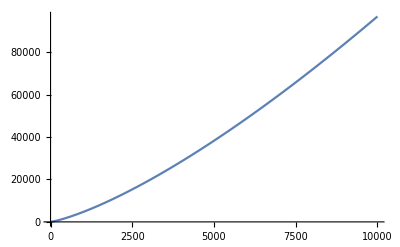

```mathematica
Plot[Pn[bn],{bn,1,10000}]
```

```mathematica
Timing[FactInt[Prime[2000]Prime[3000],{8000,40000}]]
```

{13.6015,17389}

```mathematica
Floor[1375/60]
```

```mathematica
50
```

```mathematica
5500 mins
```

5500 mins

```mathematica
Row[{1,IntegerDigits[Prime[3100000]Prime[2000000],2],22,IntegerDigits[Prime[31000000]Prime[20000000],2]}]
```

1{1,0,1,1,1,1,1,0,1,1,1,1,0,0,1,0,1,0,1,0,1,1,1,0,1,1,1,0,1,0,1,0,1,1,1,0,1,0,1,1,1,0,1,0,1,1,0,0,0,0,1}22{1,1,0,0,0,1,0,0,1,1,1,0,1,0,0,1,0,1,0,1,1,0,1,0,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,0,0,1,0,0,1,0,1,0,1,1,0,0,0,1,0,0,0,1}

```mathematica
Prime[20000000]
```

373587883

```mathematica
Test[mem,7]-Floor[Log[2,mem]]
```

1226

```mathematica
N[Log[2,Prime[20]Prime[300]]]
```

17.1061

```mathematica
{FactorInteger[915],Prime[20]}
```

{{{3,1},{5,1},{61,1}},71}